## Выполнение расчетного задания по дисциплине Тепломассообмен в среде Mathematica 14 Студент: Григорьев К.А. Группа: ТФ-11-22 Задача № 1 -Graphics-

#### Данные из условия: d2=140(mm);δ=4(mm) - геометрия труб ; tAir=2 (°C)-температура воздуха;tLiquid1=160(°C)-температура горячей воды на входе (как t_ж1) ; p=5(MPa)- давление горячей воды;w=5.2(m/s) - скорость течения горячей воды; λMinWool=0.05(W/m*K);δMinWool=30(mm); tLiquid2=160-70=90(°C)-температура горячей воды на выходе(как t_ж2) ; λConcrete=1.1(W/m K);δConcrete=50(mm);ϵ=0.8-излучательная способность поверхности материала труб; α= 11(W/m^2K)-коэффициент теплоотдачи

```mathematica
d2=140*10^-3;δ=4*10^-3;tAir=2;tLiquid1=160;p=5*10^6;w=5.2;λMinWool=0.05;δMinWool=30*10^-3;tLiquid2=90;λConcrete=1.1;δConcrete=30*10^-3;
ϵ=0.8;
α=11;
```

#### Сталь берем нержавеющую, ее коэффициент теплопроводности λSteel (W/m K) берем как const в виду слабой зависимости от температуры:

```mathematica
λSteel=14.4 ;
```

#### Изобарную (p=5MPa)теплоемкость и плотность воды при tLiquid1 и tLiquid2 найдем через REFPROP: cp: tLiquid1=160 (°C) =433.15(K) cp1=4.3204 (kJ/kg K) -Graphics-

#### tLiquid2=90 (°C) =363.15(K) cp2=4.1949 (kJ/kg K) -Graphics- плотность: tLiquid1=160 (°C) ρ1=910.03 (kg/m^3) -Graphics- tLiquid2=90 (°C) ρ2=967.50 (kg/m^3) -Graphics-

```mathematica
cp1=4.3204;cp2=4.1949 ;ρ1=910.03;ρ2=967.50 ;
```

#### Средняя удельная изобарная теплоемкость cpAverage(J/kg K)

```mathematica
cpAverage=(cp1+cp2)/2*1000
```

4257.65

#### Средняя плотность воды ρAverage (kg/m^3)

```mathematica
ρAverage=(ρ1+ρ2)/2
```

938.765

#### Массовый расход воды G(kg/s)

```mathematica
G=π*((d2-2*δ)/2)^2*w*ρAverage
```

66.8033

#### Найдем диаметры d1, d3 (m)

```mathematica
d1=d2-2δ//N
```

0.132

```mathematica
d3=d2+2δ//N
```

0.148

#### Найдем линейный коэффициент теплопередачи для трубы с ватной изоляцией KlinearMinWool (W/m K)

```mathematica
KlinearMinWool=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λMinWool)*Log[d3/d2]+1/(α*d3))
```

0.537433

#### Применяя формулу Шухова найдем расстояние(длину трубы) на котором будет выполняться условие разности температур на входе и выходе в трубу с изоляцией из минеральной ваты:

```mathematica
First[NSolve[tLiquid2==tAir+(tLiquid1-tAir)*Exp[-KlinearMinWool/(G*cpAverage)*π*x],x]]
```

{x→98591.9}

#### Таким образом длина трубы равна 98591.924m)

```mathematica
L=98591.924;
```

#### Найдем линейный коэффициент теплопередачи для трубы с бетонной изоляцией KlinearConcrete (W/m K)

```mathematica
KlinearConcrete=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/(α*d3))
```

0.751734

#### По формуле Шухова найдем температуру на выходе из трубы с бетонной изоляцией:

```mathematica
t[x_,k_]:=tAir+(tLiquid1-tAir)*Exp[-k/(G*cpAverage)*π*x]
```

```mathematica
t[L,KlinearConcrete]
```

71.6836

#### Найдем линейный коэффициент теплопередачи для трубы без изоляции KlinearRaw (W/m K)

```mathematica
KlinearRaw=1/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(α*d3))
```

0.766284

#### По формуле Шухова найдем температуру на выходе из трубы без изоляции:

```mathematica
t[L,KlinearRaw]
```

70.5882

#### Функция теплового потока и плотности теплового потока :

```mathematica
Q[x_,k_]:=k*π*(t[x,k]-tAir)*x;
qLinear[x_,k_]:=k*π*(t[x,k]-tAir);
```

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для голой трубы:

```mathematica
Q[L,KlinearRaw]
```

1.62791×10^7

```mathematica
qLinear[L,KlinearRaw]
```

165.116

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для трубы с бетонной изоляцией:

```mathematica
Q[L,KlinearConcrete]
```

1.62251×10^7

```mathematica
qLinear[L,KlinearConcrete]
```

164.568

#### Тепловой поток Q(W) и его линейная плотность qLinear(W/m) для трубы с ватной изоляцией:

```mathematica
Q[L,KlinearMinWool]
```

1.46487×10^7

```mathematica
qLinear[L,KlinearMinWool]
```

148.579

### Произведем расчеты по другому:

```mathematica
qLinearAdditional[k_]:=k*π*((tLiquid1+tLiquid2)/2-tAir)
```

#### Запишем баланс энергий: Q=qLinear*L=G*cpAverage*(tLiquid1-tLiquid2)=π *(d1/2)^2*w*cpAverage*ρAverage*(tLiquid1-tLiquid2),отсюда можно найти L(m):

```mathematica
Ladditional=First[NSolveValues[qLinearAdditional[KlinearMinWool]*x==π*(d1/2)^2*w*cpAverage*ρAverage*(tLiquid1-tLiquid2),x]]
```

95870.9

#### Выразим tLiquid2 из линейной плотности теплового потока как переменную :

```mathematica
Solve[k*π*((tLiquid2asVariable+tLiquid1)/2-tAir)*x==π*(d1/2)^2*w*cpAverage*ρAverage*(tLiquid1-tLiquid2asVariable),tLiquid2asVariable]
```

{{tLiquid2asVariable→(4.5508×10^7-245.044 k x)/(284425.+1.5708 k x)}}

```mathematica
tLiquid2asVariable[k_,x_]:=(4.550801754893684*^7-245.04422698000386 k x)/(284425.10968085524+1.5707963267948966 k x)
```

#### Теперь найдем температуры на выходе из трубы с бетонной изоляцией и трубы без изоляции. Бетонная изоляция:

```mathematica
tLiquid2asVariable[KlinearConcrete,Ladditional]
```

70.0343

#### Голая труба:

```mathematica
tLiquid2asVariable[KlinearRaw,Ladditional]
```

68.7955

#### Изобразим функциональные зависимости температуры жидкости в точке χ, где χ-обобщенное расстояние(от точки входа воды)

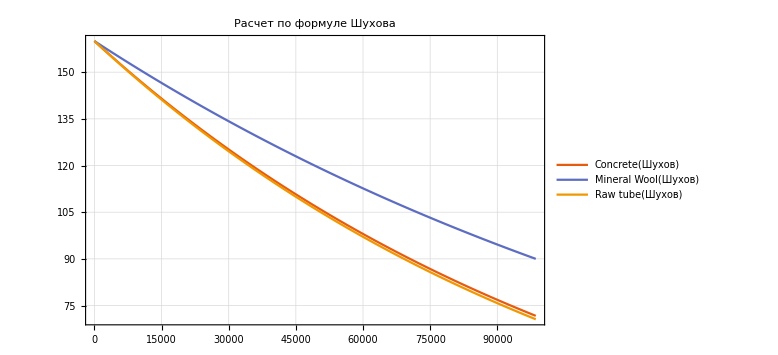

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw]},{χ,0,L},PlotLabel->"Расчет по формуле Шухова",PlotTheme->"Scientific",PlotLegends->{"Concrete(Шухов)","Mineral Wool(Шухов)","Raw tube(Шухов)"},ImageSize->Large,GridLines->Automatic]
```

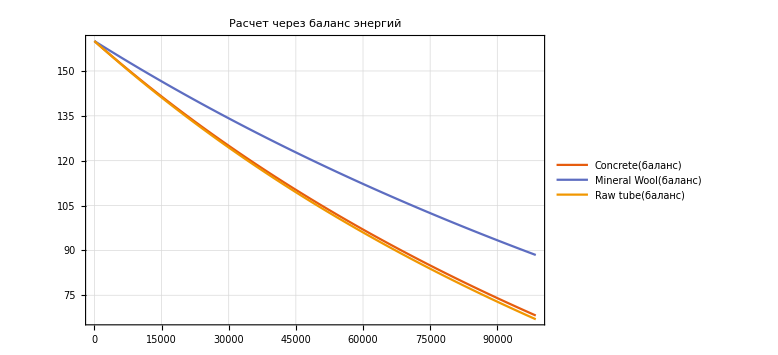

```mathematica
Plot[{tLiquid2asVariable[KlinearConcrete,χ],tLiquid2asVariable[KlinearMinWool,χ],tLiquid2asVariable[KlinearRaw,χ]},{χ,0,L},PlotLabel->"Расчет через баланс энергий",PlotTheme->"Scientific",PlotLegends->{"Concrete(баланс)","Mineral Wool(баланс)","Raw tube(баланс)"},ImageSize->Large,GridLines->Automatic]
```

#### Сопоставим функции температур в одной системе координат:

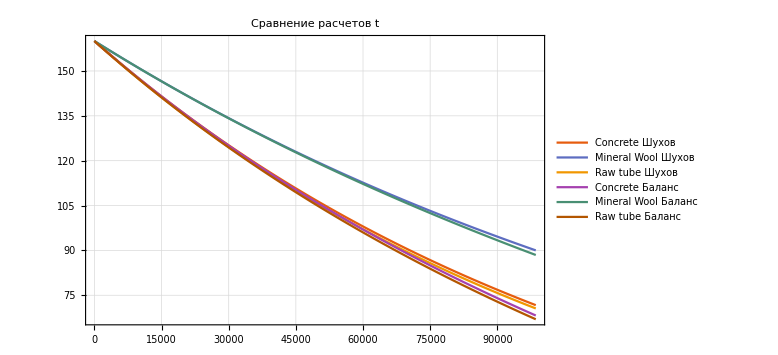

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw],tLiquid2asVariable[KlinearConcrete,χ],tLiquid2asVariable[KlinearMinWool,χ],tLiquid2asVariable[KlinearRaw,χ]},{χ,0,L},PlotLabel->"Сравнение расчетов t",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Точно так же изобразим функции линейных плотностей тепловых потоков. Для начала введем функцию линейной плотности теплового потока при расчете методом баланса энергий:

```mathematica
qLinearAdditionalFunction[k_]:=k*π*((tLiquid1-tLiquid2)/2-tAir)
```

#### Покажем графики линейных плотностей тепловых потоков в одной координатной плоскости ql(W/m):

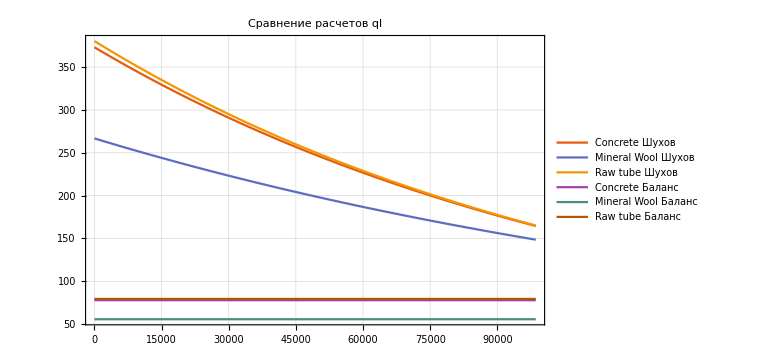

```mathematica
Plot[{qLinear[χ,KlinearConcrete],qLinear[χ,KlinearMinWool],qLinear[χ,KlinearRaw],qLinearAdditionalFunction[KlinearConcrete],qLinearAdditionalFunction[KlinearMinWool],qLinearAdditionalFunction[KlinearRaw]},{χ,0,L},PlotLabel->"Сравнение расчетов ql",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Теперь построим поверхностные плотности тепловых потоков qc (W/m^2):

```mathematica
qcShuhov[x_,k_]:=qLinear[x,k]/(π*d1);qcBalance[k_]:=qLinearAdditionalFunction[k]/(π*d1);
```

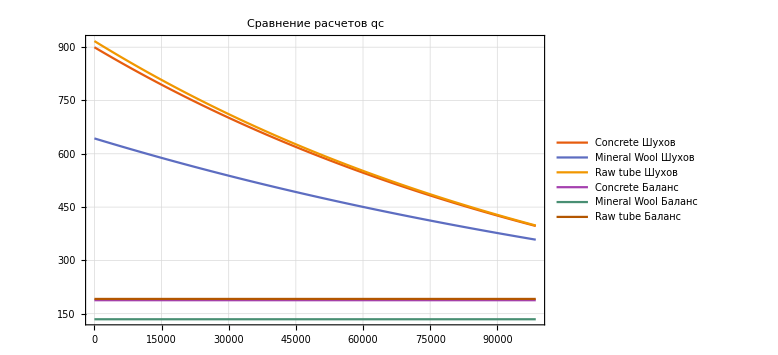

```mathematica
Plot[{qcShuhov[χ,KlinearConcrete],qcShuhov[χ,KlinearMinWool],qcShuhov[χ,KlinearRaw],qcBalance[KlinearConcrete],qcBalance[KlinearMinWool],qcBalance[KlinearRaw]},{χ,0,L},PlotLabel->"Сравнение расчетов qc",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Баланс","Mineral Wool Баланс","Raw tube Баланс"},ImageSize->Large,GridLines->Automatic]
```

#### Найдем среднее значение линейной плотности теплового потока(W/m):

```mathematica
qLinearAverageWithoutInsulation=(qLinear[0,KlinearRaw]+qLinear[L,KlinearRaw])/2
```

272.739

```mathematica
qLinearAverageConcreteInsulation=(qLinear[0,KlinearConcrete]+qLinear[L,KlinearConcrete])/2
```

268.854

```mathematica
qLinearAverageMinWoolInsulation=(qLinear[0,KlinearMinWool]+qLinear[L,KlinearMinWool])/2
```

207.673

#### Среднее значение температуры на поверхности труб:

```mathematica
{twWithoutIns,twConcreteIns,twMinWoolIns}=Flatten[NSolveValues[{qLinearAverageWithoutInsulation==π*(twWithoutInsBUFFER-tAir)/(1/(α*d2)),qLinearAverageConcreteInsulation==π*(twConcreteInsBUFFER-tAir)/(1/(α*d3)),qLinearAverageMinWoolInsulation==π*(twMinWoolInsBUFFER-tAir)/(1/(α*d3))},{twWithoutInsBUFFER,twConcreteInsBUFFER,twMinWoolInsBUFFER}]]
```

{58.3737,54.5668,42.6046}

#### Учтем излучение σ- константа Стефана-Больцмана(W/m^2 K^4)

```mathematica
σ=5.671*10^-8;
```

#### Переведем температуры на поверхности труб и температуру воздуха в абсолютные единицы(Кельвины)

```mathematica
TwWithoutIns=twWithoutIns+273.15;TwConcreteIns=twConcreteIns+273.15;TwMinWoolIns=twMinWoolIns+273.15;Tair=tAir+273.15;
```

#### Найдем результирующую плотность потока излучения Eres(W/m^2):

```mathematica
EresMinWool=ϵ*σ*(TwMinWoolIns^4-Tair^4)
```

190.938

```mathematica
EresConcrete=ϵ*σ*(TwConcreteIns^4-Tair^4)
```

263.26

```mathematica
EresWithoutIns=ϵ*σ*(TwWithoutIns^4-Tair^4)
```

288.002

#### Найдем эквивалентный коэффициент теплоотдачи излучением αEqv (W/m^2K):

```mathematica
αEqvMinWool=EresMinWool/(TwMinWoolIns-Tair)
```

4.70238

```mathematica
αEqvConcrete=EresConcrete/(TwConcreteIns-Tair)
```

5.0081

```mathematica
αEqvWithoutIns=EresWithoutIns/(TwWithoutIns-Tair)
```

5.1088

```mathematica
MradMinWool=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λMinWool)*Log[d3/d2]+1/((α+αEqvMinWool)*d3)
```

1.67675

```mathematica
MradConcrete=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvConcrete)*d3)
```

1.13809

```mathematica
MradWithoutIns=1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/((α+αEqvWithoutIns)*d3)
```

1.11019

```mathematica
P=(d1/2)^2*w*ρAverage*cpAverage
```

90535.3

```mathematica
tLiquid2RadiationVariable[M_,x_]:=(2*P*M*tLiquid1+2*tAir*x - tLiquid1*x)/(x+2*P*M)
```

#### Линейная плотность потока излучения для трубы с ватной изоляцией:

```mathematica
qLinearRadiationMinWool[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradMinWool,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvMinWool)*d3))
```

#### Из баланса энергий найдем длину трубы:

```mathematica
LwithRadiation=First[NSolveValues[((tLiquid1+tLiquid2)/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvMinWool)*d3))*Len ==π*(d1/2)^2*w*ρAverage*cpAverage*(tLiquid1-tLiquid2),Len]]
```

185551.

#### Линейная плотность потока излучения трубы с ватной изоляцией:(W/m)

```mathematica
qLinearRadiationMinWool[LwithRadiation]
```

268.763

#### Для трубы без изоляции:(W/m^2)

```mathematica
qLinearRadiationWithoutIns[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradWithoutIns,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/((α+αEqvWithoutIns)*d3))
```

```mathematica
qLinearRadiationWithoutIns[LwithRadiation]
```

232.5

```mathematica
tLiquid2RadiationVariableWithoutIns=tLiquid2RadiationVariable[MradWithoutIns,LwithRadiation]
```

8.32401

#### Для трубы с изоляцией из бетона:

```mathematica
qLinearRadiationConcrete[x_]:=π*((tLiquid1+tLiquid2RadiationVariable[MradConcrete,x])/2-tAir)/(1/(α*d1)+1/(2λSteel)*Log[d2/d1]+1/(2λConcrete)*Log[d3/d2]+1/((α+αEqvConcrete)*d3))
```

```mathematica
qLinearRadiationConcrete[LwithRadiation]
```

229.501

```mathematica
tLiquid2RadiationVariable[MradConcrete,LwithRadiation]
```

10.2804

#### Рассчитаем потери теплоты:

```mathematica
QradConcrete[x_]:=qLinearRadiationConcrete[x]*x;
QradMinWool[x_]:=qLinearRadiationMinWool[x]*x;
QradWithoutIns[x_]:=qLinearRadiationWithoutIns[x]*x;
```

#### Потери теплоты в трубе с бетонной изоляцией:(W)

```mathematica
QradConcrete[LwithRadiation]
```

4.2584×10^7

#### Потери теплоты в трубе с ватной изоляцией:(W)

```mathematica
QradMinWool[LwithRadiation]
```

4.98692×10^7

```mathematica
QradWithoutIns[LwithRadiation]
```

4.31405×10^7

#### Сравним расчеты температуры(Шухов/Излучение):

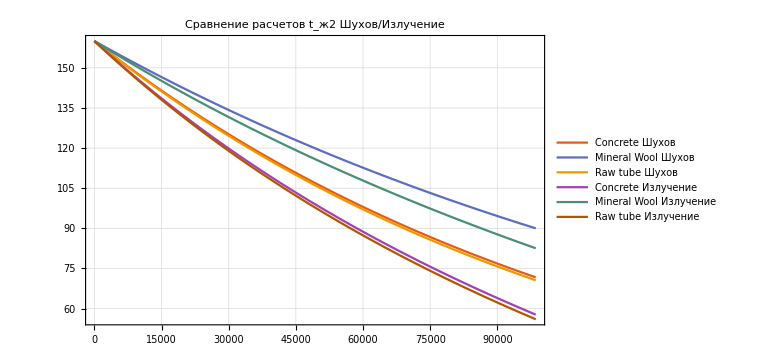

```mathematica
Plot[{t[χ,KlinearConcrete],t[χ,KlinearMinWool],t[χ,KlinearRaw],tLiquid2RadiationVariable[MradConcrete,χ],tLiquid2RadiationVariable[MradMinWool,χ],tLiquid2RadiationVariable[MradWithoutIns,χ]},{χ,0,L},PlotLabel->"Сравнение расчетов t_(:04362) Шухов/Излучение",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Излучение","Mineral Wool Излучение","Raw tube Излучение"},ImageSize->Large,GridLines->Automatic]
```

#### Сравним расчеты линейной плотности потоков тепла/излучения(Шухов/Излучение):

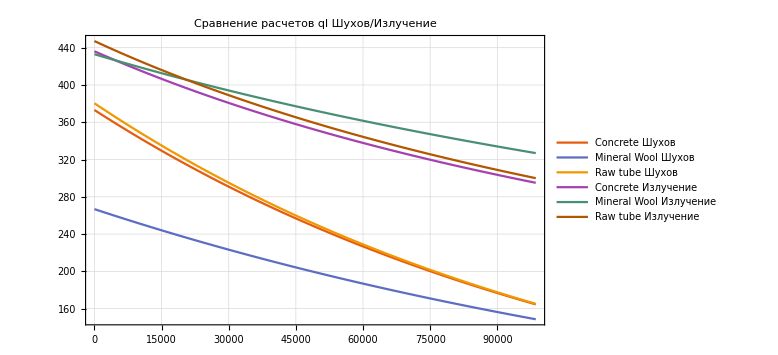

```mathematica
Plot[{qLinear[χ,KlinearConcrete],qLinear[χ,KlinearMinWool],qLinear[χ,KlinearRaw],qLinearRadiationConcrete[χ],qLinearRadiationMinWool[χ],qLinearRadiationWithoutIns[χ]},{χ,0,L},PlotLabel->"Сравнение расчетов ql Шухов/Излучение",PlotTheme->"Scientific",PlotLegends->{"Concrete Шухов","Mineral Wool Шухов","Raw tube Шухов","Concrete Излучение","Mineral Wool Излучение","Raw tube Излучение"},ImageSize->Large,GridLines->Automatic]
```

#### Соберем все результаты выше воедино. Способ основанный на формуле Шухова. Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции)

```mathematica
t[L,KlinearConcrete]
```

71.6836

```mathematica
t[L,KlinearMinWool]
```

90.

```mathematica
t[L,KlinearRaw]
```

70.5882

#### Тепловой поток(W):(порядок:бетон,вата,без изоляции)

```mathematica
Q[L,KlinearConcrete]
```

1.62251×10^7

```mathematica
Q[L,KlinearMinWool]
```

1.46487×10^7

```mathematica
Q[L,KlinearRaw]
```

1.62791×10^7

#### Способ основанный на методе баланса энергии. Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции). Очевидно что способ плохо работает. Там уже лед вытекает будто при таком расчете.

```mathematica
tLiquid2asVariable[KlinearConcrete,Ladditional]
```

70.0343

```mathematica
tLiquid2asVariable[KlinearMinWool,Ladditional]
```

90.

```mathematica
tLiquid2asVariable[KlinearRaw,Ladditional]
```

68.7955

#### Тепловой поток(W):(порядок:бетон,вата,без изоляции)

```mathematica
Qadditional[k_,x_]:=qLinear[x,k]*x;
```

```mathematica
Qadditional[KlinearConcrete,Ladditional]
```

1.61378×10^7

```mathematica
Qadditional[KlinearMinWool,Ladditional]
```

1.44763×10^7

```mathematica
Qadditional[KlinearRaw,Ladditional]
```

1.61986×10^7

#### Способ с учетом излучения.Температуры жидкости на выходе(°C):(порядок:бетон,вата,без изоляции)

```mathematica
tLiquid2RadiationVariable[MradConcrete,LwithRadiation]
```

10.2804

```mathematica
tLiquid2RadiationVariable[MradMinWool,LwithRadiation]
```

40.1334

```mathematica
tLiquid2RadiationVariable[MradWithoutIns,LwithRadiation]
```

8.32401

#### Поток излучения(W):(порядок:бетон,вата,без изоляции)

```mathematica
QradConcrete[LwithRadiation]
```

4.2584×10^7

```mathematica
QradMinWool[LwithRadiation]
```

4.98692×10^7

```mathematica
QradWithoutIns[LwithRadiation]
```

4.31405×10^7

#### Найдем критический диаметр при бетонной и ватной изоляциях

```mathematica
d2//N
```

0.14

```mathematica
dCriticalConcrete=d2+(2λConcrete)/α
```

0.34

```mathematica
dCriticalMinWool=d2+(2λMinWool)/α
```

0.149091

#### Вывод: Тепло от теплоносителя лучше всего сохраняет труба с ватной изоляцией. На втором месте бетон. На почетном третьем- труба без изоляции